# Movement detection with flicker supression

```mathematica
raw=Import[ToFileName[ParentDirectory[NotebookDirectory[]] <> "/samples/","flicker.mov"], "Data"];
```

```mathematica
nframes=Length[raw]
```

97

```mathematica
Dimensions[raw]
```

{97,480,640,3}

```mathematica
raw[[1,1,1]]
```

{255,255,255}

```mathematica
Image[raw[[1]],"Byte"]
```

-Graphics-

```mathematica
orig =Map[(#.{0.3,0.59,0.11})&,raw,{3}];
```

```mathematica
Image[orig[[1]],"Byte"]
```

-Graphics-

```mathematica
scaleFactor = 2;
```

```mathematica
meanKernel=BoxMatrix[scaleFactor]/((2*scaleFactor+1)^2);
MatrixForm[meanKernel]
```

(1/25 | 1/25 | 1/25 | 1/25 | 1/25
1/25 | 1/25 | 1/25 | 1/25 | 1/25
1/25 | 1/25 | 1/25 | 1/25 | 1/25
1/25 | 1/25 | 1/25 | 1/25 | 1/25
1/25 | 1/25 | 1/25 | 1/25 | 1/25)

```mathematica
origc=Map[ListConvolve[meanKernel,#,{-1,-1},0]& ,orig];
```

```mathematica
Image[origc[[1]],"Byte"]
```

-Graphics-

```mathematica
origdim=Dimensions[orig]
```

{97,480,640}

```mathematica
bwm=Map[Take[#,{1,origdim[[2]],scaleFactor},{1,origdim[[3]],scaleFactor}]&,origc];
```

```mathematica
Dimensions[bwm]
```

{97,240,320}

```mathematica
Manipulate[Image[bwm[[f]],"Byte"] ,{f,1,nframes,1}]
```

```mathematica
avgFrame[d_] := Total[d]/Length[d]
```

```mathematica
avgFilter[l_,w_]:= 
	Map[avgFrame[l[[Max[1,#-w];;#]]] &, Range[Length[l]]]
```

```mathematica
bwms=avgFilter[bwm,10];
```

```mathematica
Manipulate[ImageAdjust[Image[bwm[[f]]-bwms[[f]], "Byte"]],{f,1,nframes,1}]
```

```mathematica
errs = Map[RootMeanSquare[Flatten[bwm[[#]]-bwms[[#]]]] / Mean[Flatten[bwm[[#]]]]&, Range[nframes]];
```

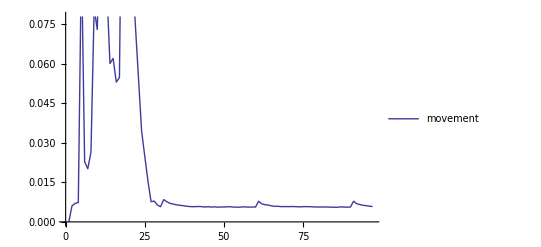

```mathematica
ListLinePlot[errs, PlotLegends ->{"movement"}]
```

```mathematica
lmsmoothPoint[d_] := Module[{data,rdata},
	data = Transpose[{Range[Length[d]],d}];
	rdata =Select[data,NumberQ[N[#[[2]]]]&];
	If[Length[rdata]<2,
		Last[d],
		Fit[rdata,{1,x},x] /. x-> Length[d]
	]
]
```

```mathematica
lmsmooth[l_,w_]:= 
	Map[lmsmoothPoint[l[[Max[1,#-w];;#]]] &, Range[Length[l]]]
```

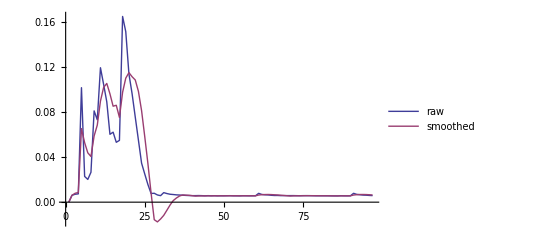

```mathematica
serrs=lmsmooth[errs,10];
ListLinePlot[{errs,serrs},PlotLegends ->{"raw","smoothed"}]
```

```mathematica
motionThreshold=0.05;
motionFlag=UnitStep[serrs-motionThreshold]
```

{0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

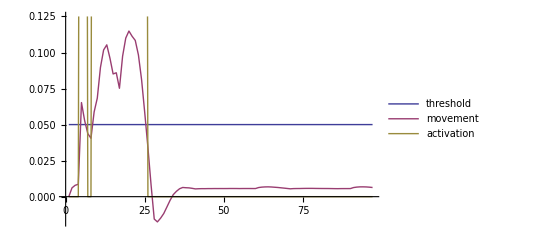

```mathematica
ListLinePlot[{Table[motionThreshold,{nframes}],serrs,motionFlag},
PlotLegends ->{"threshold","movement","activation"}
]
```